Fixpunkte des Ratengleichungssystems mit Feedback (Ν ist hier ein griechisches Nu):

```mathematica
Solve[{0==Ν S-S/τs,0==(J0+κ S-Ν)/τn-Ν S},{S,Ν}]
```

{{S→0,Ν→J0},{S→(1-J0 τs)/(-τn+κ τs),Ν→1/τs}}

Jacobi-Matrix:

```mathematica
M=FullSimplify[D[{Ν S-S/τs,(J0+κ S-Ν)/τn-Ν S},{{S,Ν}}]];
MatrixForm[M]
```

(Ν-1/τs | S
-Ν+κ/τn | -(1+S τn)/τn)

Fixpunkt x_1^* in Jacobi-Matrix einsetzen:

```mathematica
S=0;Ν=J0;
MatrixForm[M]
```

(J0-1/τs | 0
-J0+κ/τn | -1/τn)

Variablen S und Ν wieder freigeben, um zweiten Fixpunkt x_2^* einsetzen zu können:

```mathematica
S=.;Ν=.;
```

Fixpunkt x_2^* in Jacobi-Matrix einsetzen:

```mathematica
S=(1-τs J0)/(κ τs-τn);Ν=1/τs;
FullSimplify[MatrixForm[M]]
```

(0 | (-1+J0 τs)/(τn-κ τs)
κ/τn-1/τs | ((κ-J0 τn) τs)/(τn (τn-κ τs)))

Bestimmung der Eigenwerte:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
M=FullSimplify[D[{Ν S-S/τs,(J0+κ S-Ν)/τn-Ν S},{{S,Ν}}]];
FullSimplify[M];
S=(1-τs J0)/(κ τs-τn);Ν=1/τs;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1]
λ2=Part[EV,2]
```

1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2+√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))

1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2-√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))

Eigenwerte als Funktion von S schreiben (S vom zweiten Fixpunkt nach J_0 umstellen):

```mathematica
S=.;J0=(1-S(κ τs-τn))/τs;
FullSimplify[λ1]
FullSimplify[λ2]
```

((1+S τn) τs (-τn+κ τs)+√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))

((1+S τn) τs (-τn+κ τs)-√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))

Stabilitätsanalyse bezüglich J_0:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
Solve[(κ-J0 τn) τs^2+√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3))==0,J0]
Solve[(κ-J0 τn) τs^2-√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3))==0,J0]
```

{{J0→1/τs}}

{{J0→1/τs}}

Bei welchem J_0 wird die Diskriminante Null?

```mathematica
Solve[τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)==0,J0]
```

{{J0→-(-4 τn^3 τs+8 κ τn^2 τs^2-2 κ τn τs^3-4 κ^2 τn τs^3+√(4 τn^2 τs^3 (-4 τn^3+8 κ τn^2 τs-4 κ^2 τn τs^2-κ^2 τs^3)+(4 τn^3 τs-8 κ τn^2 τs^2+2 κ τn τs^3+4 κ^2 τn τs^3)^2))/(2 τn^2 τs^3)},{J0→(4 τn^3 τs-8 κ τn^2 τs^2+2 κ τn τs^3+4 κ^2 τn τs^3+√(4 τn^2 τs^3 (-4 τn^3+8 κ τn^2 τs-4 κ^2 τn τs^2-κ^2 τs^3)+(4 τn^3 τs-8 κ τn^2 τs^2+2 κ τn τs^3+4 κ^2 τn τs^3)^2))/(2 τn^2 τs^3)}}

Prüfen der Stabilität der Eigenwerte für negative Diskriminante, bzw. für komplexen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach J_0:

```mathematica
Solve[(κ-J0 τn) τs^2==0,J0]
```

{{J0→κ/τn}}

Setzen der Parameter für das Bifurkationsdiagramm λ(J_0):

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
M=FullSimplify[D[{Ν S-S/τs,(J0+κ S-Ν)/τn-Ν S},{{S,Ν}}]];
S=(1-τs J0)/(κ τs-τn);Ν=1/τs;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1];
λ2=Part[EV,2];
β=0.01;
τs=10^-2;
τn=10^-2;
```

Eigenwerte in Abhängigkeit von J_0 für verschiedene κ. Wegen Photonenkomponente des Fixpunktes S_2^* führen nur κ<1 zu physikalischen Lösungen:

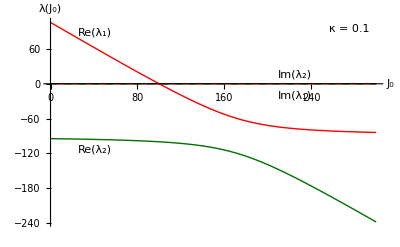

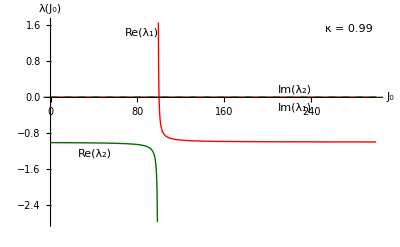

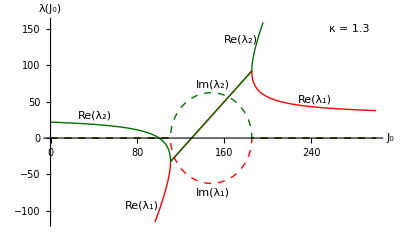

```mathematica
κ=0.1;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{J0,0,300},AxesLabel->{"J_0","λ(J_0)"},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.15,.93}]],Text["Re(λ_2)",Scaled[{.15,.37}]],Text["Im(λ_1)",Scaled[{.74,.63}]],Text["Im(λ_2)",Scaled[{.74,.73}]],Text["κ = 0.1",Scaled[{.90,.95}]]}]

κ=0.99;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{J0,0,300},AxesLabel->{"J_0","λ(J_0)"},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.29,.93}]],Text["Re(λ_2)",Scaled[{.15,.35}]],Text["Im(λ_1)",Scaled[{.74,.57}]],Text["Im(λ_2)",Scaled[{.74,.66}]],Text["κ = 0.99",Scaled[{.90,.95}]]}]

κ=1.3;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{J0,0,300},AxesLabel->{"J_0","λ(J_0)"},PlotStyle->{Red,Darker[Darker[Green]],{Red,Dashed},{Darker[Darker[Green]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.29,.10}]],Text["Re(λ_1)",Scaled[{.80,.61}]],Text["Re(λ_2)",Scaled[{.15,.53}]],Text["Re(λ_2)",Scaled[{.58,.90}]],Text["Im(λ_1)",Scaled[{.50,.16}]],Text["Im(λ_2)",Scaled[{.50,.68}]],Text["κ = 1.3",Scaled[{.90,.95}]]}]

Manipulate[Plot[{Re[1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2+√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))],Re[1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2-√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))],Im[1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2+√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))],Im[1/(2 τn τs (τn-κ τs))((κ-J0 τn) τs^2-√(τs (4 τn^3-4 τn^2 (2 κ+J0 τn) τs+4 κ τn (κ+2 J0 τn) τs^2+(κ^2-2 J0 κ (1+2 κ) τn+J0^2 τn^2) τs^3)))]},{J0,0,500},AxesLabel->{"J_0","λ(J_0)"},PlotRange->{{0,500},{-200,100}}],{{κ,0,"κ"},-0.50,2,Appearance->"Labeled"}]
```

Stabilitätsanalyse bezüglich S:
Prüfen der Stabilität der Eigenwerte für positive Diskriminante, bzw. für reelen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach S:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
Solve[-(1+S τn) τs +√(τs^2+τs τn S (τs(4 κ+S τn+2)-4τn))==0,S]
Solve[-(1+S τn) τs-√(τs^2+τs τn S (τs(4 κ+S τn+2)-4τn))==0,S]
```

{{S→0}}

{{S→0}}

Bei welchem S wird die Diskriminante Null?

```mathematica
Solve[τs^2+τs τn S (τs(4 κ+S τn+2)-4τn)==0,S]
```

{{S→(4 τn^2-2 τn τs-4 κ τn τs-√(-4 τn^2 τs^2+(-4 τn^2+2 τn τs+4 κ τn τs)^2))/(2 τn^2 τs)},{S→(4 τn^2-2 τn τs-4 κ τn τs+√(-4 τn^2 τs^2+(-4 τn^2+2 τn τs+4 κ τn τs)^2))/(2 τn^2 τs)}}

Prüfen der Stabilität der Eigenwerte für negative Diskriminante, bzw. für komplexen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach S:

```mathematica
Solve[-(1+S τn) τs ==0,S]
```

{{S→-1/τn}}

Setzen der Parameter für das Bifurkationsdiagramm λ(S):

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
M=FullSimplify[D[{Ν S-S/τs,(J0+κ S-Ν)/τn-Ν S},{{S,Ν}}]];
S=(1-τs J0)/(κ τs-τn);Ν=1/τs;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1];
λ2=Part[EV,2];
S=.;J0=(1-S(κ τs-τn))/τs;
FullSimplify[λ1];
FullSimplify[λ2];
β=0.01;
τs=10^-2;
τn=10^-2;
```

Eigenwerte in Abhängigkeit von S für verschiedene κ:

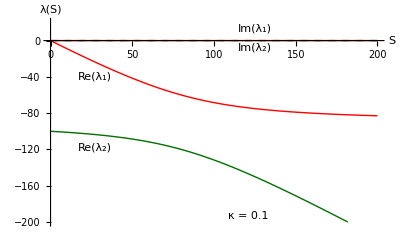

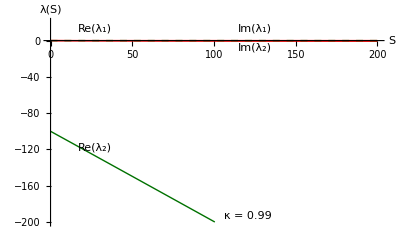

```mathematica
κ=0.1;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{S,0,200},AxesLabel->{"S","λ(S)"},PlotRange->{{0,200},{-200,20}},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["κ = 0.1",Scaled[{.60,.05}]],Text["Re(λ_1)",Scaled[{.15,.72}]],Text["Re(λ_2)",Scaled[{.15,.38}]],Text["Im(λ_1)",Scaled[{.62,.95}]],Text["Im(λ_2)",Scaled[{.62,0.86}]]}]

κ=0.99;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{S,0,200},AxesLabel->{"S","λ(S)"},PlotRange->{{0,200},{-200,20}},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["κ = 0.99",Scaled[{.60,.05}]],Text["Re(λ_1)",Scaled[{.15,.95}]],Text["Re(λ_2)",Scaled[{.15,.38}]],Text["Im(λ_1)",Scaled[{.62,.95}]],Text["Im(λ_2)",Scaled[{.62,0.86}]]}]

Manipulate[Plot[{Re[1/(2 τn τs (τn-κ τs))((1+S τn) τs (-τn+κ τs)+√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))],Re[1/(2 τn τs (τn-κ τs))((1+S τn) τs (-τn+κ τs)-√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))],Im[1/(2 τn τs (τn-κ τs))((1+S τn) τs (-τn+κ τs)+√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))],Im[1/(2 τn τs (τn-κ τs))((1+S τn) τs (-τn+κ τs)-√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))]},{S,0,500},AxesLabel->{"S","λ(S)"},PlotRange->{{0,500},{-600,100}}],{{κ,0,"κ"},-0.5,0.99,Appearance->"Labeled"}]
```

Stabilitätsanalyse bezüglich κ:
Prüfen der Stabilität der Eigenwerte für positive Diskriminante, bzw. für reelen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach κ:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
Solve[-(1+S τn) τs +√(τs^2+τs τn S (τs(4 κ+S τn+2)-4τn))==0,κ]
Solve[-(1+S τn) τs +√(τs^2+τs τn S (τs(4 κ+S τn+2)-4τn))==0,κ]
```

{{κ→τn/τs}}

{{κ→τn/τs}}

Bei welchem κ wird die Diskriminante Null?

```mathematica
Solve[τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))==0,κ]
```

{{κ→τn/τs},{κ→τn/τs},{κ→(4 S τn^2-τs-2 S τn τs-S^2 τn^2 τs)/(4 S τn τs)}}

Prüfen der Stabilität der Eigenwerte für negative Diskriminante, bzw. für komplexen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach κ:

```mathematica
Solve[(1+S τn) τs (-τn+κ τs)==0,κ]
```

{{κ→τn/τs}}

Setzen der Parameter für das Bifurkationsdiagramm λ(κ):

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
M=FullSimplify[D[{Ν S-S/τs,(J0+κ S-Ν)/τn-Ν S},{{S,Ν}}]];
S=(1-τs J0)/(κ τs-τn);Ν=1/τs;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1];
λ2=Part[EV,2];
S=.;J0=(1-S(κ τs-τn))/τs;
FullSimplify[λ1];
FullSimplify[λ2];
β=0.01;
τs=10^-2;
τn=10^-2;
```

Eigenwerte in Abhängigkeit von κ für verschiedene S:

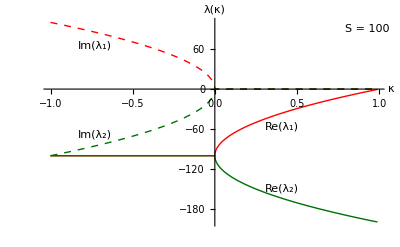

```mathematica
S=100;
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{κ,-1,0.99},AxesLabel->{"κ","λ(κ)"},PlotStyle->{Red,Darker[Darker[Green]],{Red,Dashed},{Darker[Darker[Green]],Dashed}},Epilog->{Text["S = 100",Scaled[{.95,.95}]],Text["Re(λ_1)",Scaled[{.70,.48}]],Text["Re(λ_2)",Scaled[{.70,.18}]],Text["Im(λ_1)",Scaled[{.15,.87}]],Text["Im(λ_2)",Scaled[{.15,0.44}]]}]
Manipulate[Plot[{Re[((1+S τn) τs (-τn+κ τs)+√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))],Re[((1+S τn) τs (-τn+κ τs)-√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))],Im[((1+S τn) τs (-τn+κ τs)+√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))],Im[((1+S τn) τs (-τn+κ τs)-√(τs (τn-κ τs)^2 (τs+S τn (-4 τn+(2+4 κ+S τn) τs))))/(2 τn τs (τn-κ τs))]},{κ,-1,1},AxesLabel->{"κ","λ(κ)"}],{{S,100,"S"},0,500,Appearance->"Labeled"}]
```

Zeitverläufe S(t) und Ν(t), Phasenraumportrait S(Ν) mit Berücksichtigung des Terms für spontane Emission:

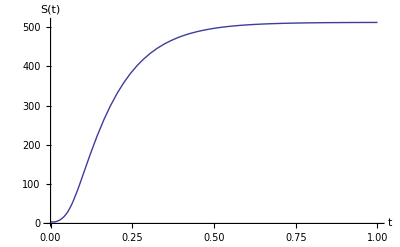

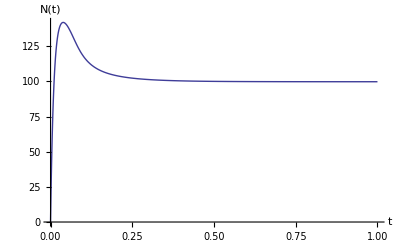

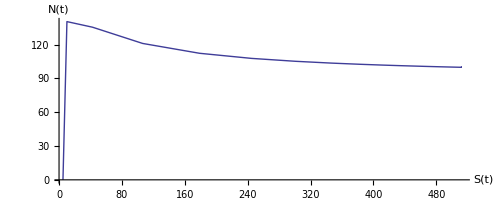

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
β=0.01;
τs=10^-2;
τn=10^-2;
J0=150;
κ=0.9;
tmax=100;
Sfix=(1-τs J0)/(κ τs-τn);Νfix=1/τs;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
s=NDSolve[{S'[t]==Ν[t] S[t]-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+κ S[t]-Ν[t])/τn-Ν[t] S[t],S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev},{S,Ν},{t,0,tmax}];
Plot[Evaluate[S[t]/.s],{t,0,tmax/100},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax/100},AxesLabel->{"t","N(t)"},PlotRange->All]
ParametricPlot[Evaluate[{S[t],Ν[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)"},PlotRange->All]
```

Input-Output Kurve:

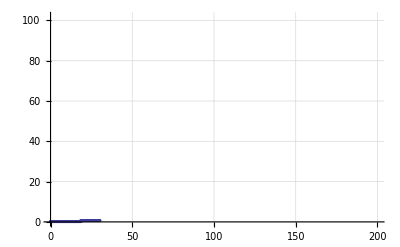

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
β=0.01;
τs=10^-2;
τn=10^-2;
κ=0;
tmax=100;
Jmax=200;
step=0.1;
Sfix=0.01;Νfix=J0;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
a=Range[0];

ProgressIndicator[Dynamic[J0],{0,Jmax}]
Do[s=NDSolve[{S'[t]==Ν[t] S[t]-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+κ S[t]-Ν[t])/τn-Ν[t] S[t],S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev},{S,Ν},{t,0,tmax}];a=Flatten[Append[a,{J0,Evaluate[S[tmax]/.s]}]],{J0,0,Jmax,step}];
io=Partition[a,2];
ListPlot[io,AxesLabel->{"J_0","S(J_0)"},PlotMarkers->{●,3},GridLines->Automatic]
```